```mathematica
a={{a11,a12,a13},{a21,a22,a23},{a31,a32,a33}};
Transpose[a].a//MatrixForm
Eigenvalues[{{0.86,1.72},{2.28,0.96}}]
```

(a11^2+a21^2+a31^2 | a11 a12+a21 a22+a31 a32 | a11 a13+a21 a23+a31 a33
a11 a12+a21 a22+a31 a32 | a12^2+a22^2+a32^2 | a12 a13+a22 a23+a32 a33
a11 a13+a21 a23+a31 a33 | a12 a13+a22 a23+a32 a33 | a13^2+a23^2+a33^2)

{2.89093,-1.07093}

1.6984 x^2-4.11253 x y+2.79351 y^2

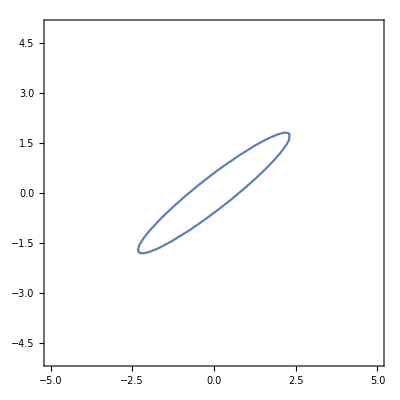

Transpose::nmtx: The first two levels of {{x1, x2}, y} cannot be transposed.

Dot::rect: Nonrectangular tensor encountered.

Transpose[{{x1,x2},y}].{{1.6984,-2.05627},{-2.05627,2.79351}}.{{x1,x2},y}

```mathematica
xv={x,y};
p={{5.410984848484818,3.982954545454517},{3.982954545454517,3.289772727272697}};
Simplify[Transpose[xv].Inverse[p].xv]
ContourPlot[Transpose[xv].Inverse[p].xv==1,{x,-5,5},{y,-5,5}]
```

```mathematica
b={{7},{3}};
a={{-6,2},{3,-5}};
x1={{1},{1}};

t1=1;
g=Integrate[MatrixExp[a t].b.Transpose[b].MatrixExp[Transpose[a t]],{t,0,t1}];

g=N[g];

FullSimplify[Transpose[b].MatrixExp[Transpose[a] (t1-t)].Inverse[g].x1]//MatrixForm

N[Sqrt[Integrate[Power[Transpose[b].MatrixExp[Transpose[a] (t1-t)].Inverse[g].x1,2],{t,0,1.1196826}]]]
```

(0.150755 ⅇ^(3 t)-0.00111964 ⅇ^(8 t))

{{1.}}

```mathematica
q1=ω^4+73ω^2+576;
q2=192ω^2+3048;
q3=701ω+28ω^3;
q4=-12ω^2+8472;
q5=31ω^3+3139ω;
res=Simplify[(q2/q1)^2+(q3/q1)^2+(q4/q1)^2+(q5/q1)^2]
Sqrt[(1/2Pi) Integrate[res,{ω,-Infinity,Infinity}]]
```

(81065088+11311826 ω^2+270882 ω^4+1745 ω^6)/((576+73 ω^2+ω^4)^2)

1/22 √(11073151/66) π

```mathematica
Sqrt[(1/2Pi) Integrate[(81065088+11311826 s^2+270882 s^4+1745 s^6)/((576+73 s^2+s^4)^2),{s,-Infinity,Infinity}]]
```

1/22 √(11073151/66) π

```mathematica
N[1/22 √(11073151/66) π]
```

58.4912

```mathematica
W={{(29 I ω+127)/(-ω^2+11 I ω+24)},{(31 I ω+353)/(-ω^2+11 I ω+24)}};
singularValue=SingularValueList[W][[1]];
singularValue=Simplify[√(((127+29 ⅈ ω) (127-29 ⅈ ω))/((24+11 ⅈ ω-ω^2) (24-11 ⅈ ω-ω^2))+((353+31 ⅈ ω) (353-31 ⅈ ω))/((24+11 ⅈ ω-ω^2) (24-11 ⅈ ω-ω^2)))]
res=N[MaxValue[singularValue,ω]]
```

√2 √((70369+901 ω^2)/(576+73 ω^2+ω^4))

15.6313

```mathematica
W={{(29 I ω+127)/(-ω^2+11 I ω+24)},{(31 I ω+353)/(-ω^2+11 I ω+24)}};
d=Expand[(-ω^2+11 I ω+24) (-ω^2-11 I ω+24)]
n1=Expand[(29 I ω+127) (-ω^2-11 I ω+24) ]
n2=Expand[(31 I ω+353) (-ω^2-11 I ω+24) ]
```

576+73 ω^2+ω^4

3048-701 ⅈ ω+192 ω^2-29 ⅈ ω^3

8472-3139 ⅈ ω-12 ω^2-31 ⅈ ω^3

```mathematica
W1amp=((3048+192 ω^2)/(576+73 ω^2+ω^4))^2+((-701 ω-29 ω^3)/(576+73 ω^2+ω^4))^2;
W2amp=((8472-12 ω^2)/(576+73 ω^2+ω^4))^2+((-3139 ω-31 ω^3)/(576+73 ω^2+ω^4))^2;
trace=Simplify[W1amp+W2amp]
res=Sqrt[ Integrate[trace,{ω,-Infinity,Infinity}]/(2Pi)]
N[%]
```

(2 (70369+901 ω^2))/(576+73 ω^2+ω^4)

(√(8363/6))/2

18.667

```mathematica
c2={{2,-1},{7,0},{0,0}};
d2={{0},{0},{3}};
k={{-2.4267, -2.2281}};
a={{0,1},{0,0}};
b2={{0},{1}};
b1={{-2,1},{1/2,3}};
Simplify[(c2+d2.k).Inverse[s*IdentityMatrix[2]-a-b2.k].b1]//MatrixForm
```

(0.-12.7658/(2.4267+2.2281 s+s^2)-(4.5 s)/(2.4267+2.2281 s+s^2) | 0.+12.8829/(2.4267+2.2281 s+s^2)-(1. s)/(2.4267+2.2281 s+s^2)
0.-27.6934/(2.4267+2.2281 s+s^2)-(14. s)/(2.4267+2.2281 s+s^2) | 0.+36.5967/(2.4267+2.2281 s+s^2)+(7. s)/(2.4267+2.2281 s+s^2)
0.-3.64005/(2.4267+2.2281 s+s^2)+(11.218 s)/(2.4267+2.2281 s+s^2) | 0.-21.8403/(2.4267+2.2281 s+s^2)-(27.333 s)/(2.4267+2.2281 s+s^2))

```mathematica
a={{0,1},{0,0}};
b1={{-2,1,0},{1/2,3,0}};
b2={{0},{1}};
c1={{1,0}};
d1={{0,0,2}};
c2={{0,0},{2,3}};
d2={{-2},{0}};
k={{-1,-2.0616}};
l={{-2.0716},{-1.5207}};

q1=Inverse[s*IdentityMatrix[2]-a];
q2=Inverse[s*IdentityMatrix[2]-a-b2.k-l.c1];
q3=Inverse[IdentityMatrix[2]+q1.b2.k.q2.l.c1 ];
q4=b1-b2.k.q2.l.d1;
q5=c2.q3.q1.q4;

q6=Inverse[IdentityMatrix[2]+q2.l.c1.q1.b2.k];
q7=l.c1.q1.b1+l.d1;
q8=-d2.k.q6.q2.q7;

q9=Simplify[q5+q8];

res={{(1.5206999999999997 s^2 (6.79151056+4.1332 s+s^2))/(-3.552713678800501*^-15+10.327850108591997 s^2+41.64654629996926 s^3+69.16554529257552 s^4+61.348018013184 s^5+30.666363360000002 s^6+8.2664 s^7+1. s^8)-(0.876124879999999 s^3 (6.79151056+4.1332 s+s^2))/(-3.552713678800501*^-15+10.327850108591997 s^2+41.64654629996926 s^3+69.16554529257552 s^4+61.348018013184 s^5+30.666363360000002 s^6+8.2664 s^7+1. s^8)-(20.82670048 s^4 (6.79151056+4.1332 s+s^2))/(-3.552713678800501*^-15+10.327850108591997 s^2+41.64654629996926 s^3+69.16554529257552 s^4+61.348018013184 s^5+30.666363360000002 s^6+8.2664 s^7+1. s^8),(9.124200000000009 s^2 (6.79151056+4.1332 s+s^2))/(-3.552713678800501*^-15+10.327850108591997 s^2+41.64654629996926 s^3+69.16554529257552 s^4+61.348018013184 s^5+30.666363360000002 s^6+8.2664 s^7+1. s^8)+(34.28145072 s^3 (6.79151056+4.1332 s+s^2))/(-3.552713678800501*^-15+10.327850108591997 s^2+41.64654629996926 s^3+69.16554529257552 s^4+61.348018013184 s^5+30.666363360000002 s^6+8.2664 s^7+1. s^8)+(10.41335024 s^4 (6.79151056+4.1332 s+s^2))/(-3.552713678800501*^-15+10.327850108591997 s^2+41.64654629996926 s^3+69.16554529257552 s^4+61.348018013184 s^5+30.666363360000002 s^6+8.2664 s^7+1. s^8),(6.082799999999999 s^4 (6.79151056+4.1332 s+s^2))/(-3.552713678800501*^-15+10.327850108591997 s^2+41.64654629996926 s^3+69.16554529257552 s^4+61.348018013184 s^5+30.666363360000002 s^6+8.2664 s^7+1. s^8)+(20.82670048 s^5 (6.79151056+4.1332 s+s^2))/(-3.552713678800501*^-15+10.327850108591997 s^2+41.64654629996926 s^3+69.16554529257552 s^4+61.348018013184 s^5+30.666363360000002 s^6+8.2664 s^7+1. s^8)},{15.915710559999997/(1.5206999999999997+5.20667512 s+6.79151056 s^2+4.1332 s^3+s^4)+(18.39447432 s)/(1.5206999999999997+5.20667512 s+6.79151056 s^2+4.1332 s^3+s^4)-(9.333000000000002 s^2)/(1.5206999999999997+5.20667512 s+6.79151056 s^2+4.1332 s^3+s^4)-(2.5 s^3)/(1.5206999999999997+5.20667512 s+6.79151056 s^2+4.1332 s^3+s^4),36.18696336/(1.5206999999999997+5.20667512 s+6.79151056 s^2+4.1332 s^3+s^4)+(83.8857908 s)/(1.5206999999999997+5.20667512 s+6.79151056 s^2+4.1332 s^3+s^4)+(51.4652 s^2)/(1.5206999999999997+5.20667512 s+6.79151056 s^2+4.1332 s^3+s^4)+(11. s^3)/(1.5206999999999997+5.20667512 s+6.79151056 s^2+4.1332 s^3+s^4),6.082799999999999/(1.5206999999999997+5.20667512 s+6.79151056 s^2+4.1332 s^3+s^4)-(29.950900479999998 s)/(1.5206999999999997+5.20667512 s+6.79151056 s^2+4.1332 s^3+s^4)-(31.24005072 s^2)/(1.5206999999999997+5.20667512 s+6.79151056 s^2+4.1332 s^3+s^4)}};

Simplify[res]//MatrixForm
```

((s^2 (10.3279+0.335146 s-143.545 s^2-86.957 s^3-20.8267 s^4))/(-3.55271×10^-15+10.3279 s^2+41.6465 s^3+69.1655 s^4+61.348 s^5+30.6664 s^6+8.2664 s^7+1. s^8) | (s^2 (61.9671+270.535 s+221.539 s^2+77.3219 s^3+10.4134 s^4))/(-3.55271×10^-15+10.3279 s^2+41.6465 s^3+69.1655 s^4+61.348 s^5+30.6664 s^6+8.2664 s^7+1. s^8) | (s^4 (41.3114+166.586 s+92.1637 s^2+20.8267 s^3))/(-3.55271×10^-15+10.3279 s^2+41.6465 s^3+69.1655 s^4+61.348 s^5+30.6664 s^6+8.2664 s^7+1. s^8)
(15.9157+18.3945 s-9.333 s^2-2.5 s^3)/(1.5207+5.20668 s+6.79151 s^2+4.1332 s^3+s^4) | (36.187+83.8858 s+51.4652 s^2+11. s^3)/(1.5207+5.20668 s+6.79151 s^2+4.1332 s^3+s^4) | (6.0828-29.9509 s-31.2401 s^2)/(1.5207+5.20668 s+6.79151 s^2+4.1332 s^3+s^4))

```mathematica
a={{0,1},{0,0}};
b1={{-2,1,0},{1/2,3,0}};
b2={{0},{1}};
c1={{1,0}};
d1={{0,0,2}};
c2={{6,-4},{0,0}};
d2={{0},{1}};
k={{-6,-5.2915}};
l={{-2.0716},{-1.5207}};

q1=Inverse[s*IdentityMatrix[2]-a];
q2=Inverse[s*IdentityMatrix[2]-a-b2.k-l.c1];
q3=Inverse[IdentityMatrix[2]+q1.b2.k.q2.l.c1 ];
q4=b1-b2.k.q2.l.d1;
q5=c2.q3.q1.q4;

q6=Inverse[IdentityMatrix[2]+q2.l.c1.q1.b2.k];
q7=l.c1.q1.b1+l.d1;
q8=-d2.k.q6.q2.q7;

q9=Simplify[q5+q8];

res={{-(17.54588579999998/(9.124199999999998+20.47638405 s+18.4825714 s^2+7.3631 s^3+s^4))-(400.47777199999996 s)/(9.124199999999998+20.47638405 s+18.4825714 s^2+7.3631 s^3+s^4)-(100.0834 s^2)/(9.124199999999998+20.47638405 s+18.4825714 s^2+7.3631 s^3+s^4)-(14. s^3)/(9.124199999999998+20.47638405 s+18.4825714 s^2+7.3631 s^3+s^4),369.18308520000005/(9.124199999999998+20.47638405 s+18.4825714 s^2+7.3631 s^3+s^4)+(103.54590779999998 s)/(9.124199999999998+20.47638405 s+18.4825714 s^2+7.3631 s^3+s^4)-(26.178600000000003 s^2)/(9.124199999999998+20.47638405 s+18.4825714 s^2+7.3631 s^3+s^4)-(6. s^3)/(9.124199999999998+20.47638405 s+18.4825714 s^2+7.3631 s^3+s^4),-(109.49039999999998/(9.124199999999998+20.47638405 s+18.4825714 s^2+7.3631 s^3+s^4))-(172.72300860000001 s)/(9.124199999999998+20.47638405 s+18.4825714 s^2+7.3631 s^3+s^4)+(163.8110724 s^2)/(9.124199999999998+20.47638405 s+18.4825714 s^2+7.3631 s^3+s^4)},{-1.5055377389217187*^-15/(9.094947017729282*^-13+2.2737367544323206*^-13 s+168.6386779678803 s^2+445.6386272379463 s^3+501.49930895465303 s^4+292.65442700068 s^5+91.18038441 s^6+14.7262 s^7+s^8)-(1.40047773555807*^-13 s)/(9.094947017729282*^-13+2.2737367544323206*^-13 s+168.6386779678803 s^2+445.6386272379463 s^3+501.49930895465303 s^4+292.65442700068 s^5+91.18038441 s^6+14.7262 s^7+s^8)-(84.31933898393939 s^2)/(9.094947017729282*^-13+2.2737367544323206*^-13 s+168.6386779678803 s^2+445.6386272379463 s^3+501.49930895465303 s^4+292.65442700068 s^5+91.18038441 s^6+14.7262 s^7+s^8)+(114.45804231678672 s^3)/(9.094947017729282*^-13+2.2737367544323206*^-13 s+168.6386779678803 s^2+445.6386272379463 s^3+501.49930895465303 s^4+292.65442700068 s^5+91.18038441 s^6+14.7262 s^7+s^8)+(811.3303227766148 s^4)/(9.094947017729282*^-13+2.2737367544323206*^-13 s+168.6386779678803 s^2+445.6386272379463 s^3+501.49930895465303 s^4+292.65442700068 s^5+91.18038441 s^6+14.7262 s^7+s^8)+(309.54953477211 s^5)/(9.094947017729282*^-13+2.2737367544323206*^-13 s+168.6386779678803 s^2+445.6386272379463 s^3+501.49930895465303 s^4+292.65442700068 s^5+91.18038441 s^6+14.7262 s^7+s^8)+(40.9527681 s^6)/(9.094947017729282*^-13+2.2737367544323206*^-13 s+168.6386779678803 s^2+445.6386272379463 s^3+501.49930895465303 s^4+292.65442700068 s^5+91.18038441 s^6+14.7262 s^7+s^8),-9.033226433530312*^-15/(9.094947017729282*^-13+2.2737367544323206*^-13 s+168.6386779678803 s^2+445.6386272379463 s^3+501.49930895465303 s^4+292.65442700068 s^5+91.18038441 s^6+14.7262 s^7+s^8)-(8.794306225468064*^-13 s)/(9.094947017729282*^-13+2.2737367544323206*^-13 s+168.6386779678803 s^2+445.6386272379463 s^3+501.49930895465303 s^4+292.65442700068 s^5+91.18038441 s^6+14.7262 s^7+s^8)-(505.9160339036402 s^2)/(9.094947017729282*^-13+2.2737367544323206*^-13 s+168.6386779678803 s^2+445.6386272379463 s^3+501.49930895465303 s^4+292.65442700068 s^5+91.18038441 s^6+14.7262 s^7+s^8)-(1505.5545596817187 s^3)/(9.094947017729282*^-13+2.2737367544323206*^-13 s+168.6386779678803 s^2+445.6386272379463 s^3+501.49930895465303 s^4+292.65442700068 s^5+91.18038441 s^6+14.7262 s^7+s^8)-(925.3202174336113 s^4)/(9.094947017729282*^-13+2.2737367544323206*^-13 s+168.6386779678803 s^2+445.6386272379463 s^3+501.49930895465303 s^4+292.65442700068 s^5+91.18038441 s^6+14.7262 s^7+s^8)-(221.32301554855502 s^5)/(9.094947017729282*^-13+2.2737367544323206*^-13 s+168.6386779678803 s^2+445.6386272379463 s^3+501.49930895465303 s^4+292.65442700068 s^5+91.18038441 s^6+14.7262 s^7+s^8)-(20.47638405 s^6)/(9.094947017729282*^-13+2.2737367544323206*^-13 s+168.6386779678803 s^2+445.6386272379463 s^3+501.49930895465303 s^4+292.65442700068 s^5+91.18038441 s^6+14.7262 s^7+s^8),-(6.022150955686875*^-15 s^2)/(9.094947017729282*^-13+2.2737367544323206*^-13 s+168.6386779678803 s^2+445.6386272379463 s^3+501.49930895465303 s^4+292.65442700068 s^5+91.18038441 s^6+14.7262 s^7+s^8)-(5.842796980459753*^-13 s^3)/(9.094947017729282*^-13+2.2737367544323206*^-13 s+168.6386779678803 s^2+445.6386272379463 s^3+501.49930895465303 s^4+292.65442700068 s^5+91.18038441 s^6+14.7262 s^7+s^8)+(7.266010015882784*^-14 s^4)/(9.094947017729282*^-13+2.2737367544323206*^-13 s+168.6386779678803 s^2+445.6386272379463 s^3+501.49930895465303 s^4+292.65442700068 s^5+91.18038441 s^6+14.7262 s^7+s^8)-(18.248399999999997 s^4 (18.4825714+7.3631 s+s^2))/(9.094947017729282*^-13+2.2737367544323206*^-13 s+168.6386779678803 s^2+445.6386272379463 s^3+501.49930895465303 s^4+292.65442700068 s^5+91.18038441 s^6+14.7262 s^7+s^8)-(40.9527681 s^5 (18.4825714+7.3631 s+s^2))/(9.094947017729282*^-13+2.2737367544323206*^-13 s+168.6386779678803 s^2+445.6386272379463 s^3+501.49930895465303 s^4+292.65442700068 s^5+91.18038441 s^6+14.7262 s^7+s^8)}};
res=Simplify[res];
res={{(-17.54588579999998-400.47777199999996 s-100.0834 s^2-14. s^3)/(9.124199999999998+20.47638405 s+18.4825714 s^2+7.3631 s^3+s^4),(369.18308520000005+103.54590779999998 s-26.178600000000003 s^2-6. s^3)/(9.124199999999998+20.47638405 s+18.4825714 s^2+7.3631 s^3+s^4),(-109.49039999999998-172.72300860000001 s+163.8110724 s^2)/(9.124199999999998+20.47638405 s+18.4825714 s^2+7.3631 s^3+s^4)},{(-84.31933898393937 s^2+114.4580423167867 s^3+811.3303227766148 s^4+309.54953477211 s^5+40.9527681 s^6)/(168.6386779678803 s^2+445.6386272379463 s^3+501.49930895465303 s^4+292.65442700068 s^5+91.18038441 s^6+14.7262 s^7+s^8),(-505.9160339036402 s^2-1505.5545596817185 s^3-925.3202174336113 s^4-221.32301554855502 s^5-20.47638405 s^6)/(168.6386779678803 s^2+445.6386272379463 s^3+501.49930895465303 s^4+292.65442700068 s^5+91.18038441 s^6+14.7262 s^7+s^8),(s^2 (-337.27735593575983 s^2-891.2772544758924 s^3-319.78772679711 s^4-40.9527681 s^5))/(168.6386779678803 s^2+445.6386272379463 s^3+501.49930895465303 s^4+292.65442700068 s^5+91.18038441 s^6+14.7262 s^7+s^8)}};
Simplify[res]//MatrixForm
```

((-17.5459-400.478 s-100.083 s^2-14. s^3)/(9.1242+20.4764 s+18.4826 s^2+7.3631 s^3+s^4) | (369.183+103.546 s-26.1786 s^2-6. s^3)/(9.1242+20.4764 s+18.4826 s^2+7.3631 s^3+s^4) | (-109.49-172.723 s+163.811 s^2)/(9.1242+20.4764 s+18.4826 s^2+7.3631 s^3+s^4)
(-84.3193+114.458 s+811.33 s^2+309.55 s^3+40.9528 s^4)/(168.639+445.639 s+501.499 s^2+292.654 s^3+91.1804 s^4+14.7262 s^5+s^6) | (-505.916-1505.55 s-925.32 s^2-221.323 s^3-20.4764 s^4)/(168.639+445.639 s+501.499 s^2+292.654 s^3+91.1804 s^4+14.7262 s^5+s^6) | -(40.9528 s^2 (8.23576+21.7635 s+7.8087 s^2+1. s^3))/(168.639+445.639 s+501.499 s^2+292.654 s^3+91.1804 s^4+14.7262 s^5+s^6))

```mathematica
Expand[-40.9527681 s^2 (8.235764554722733+21.76354116770662 s+7.808696252625473 s^2+1. s^3)]
```

-337.277 s^2-891.277 s^3-319.788 s^4-40.9528 s^5

```mathematica
a={{0,1},{0,0}};
b1={{-2,1,0},{1/2,3,0}};
b2={{0},{1}};
c1={{1,0}};
d1={{0,0,2}};
c2={{2,-1},{7,0},{0,0}};
d2={{0},{0},{3}};
k={{-2.4267,-2.2281}};
l={{-2.0716},{-1.5207}};

q1=Inverse[s*IdentityMatrix[2]-a];
q2=Inverse[s*IdentityMatrix[2]-a-b2.k-l.c1];
q3=Inverse[IdentityMatrix[2]+q1.b2.k.q2.l.c1 ];
q4=b1-b2.k.q2.l.d1;
q5=c2.q3.q1.q4;

q6=Inverse[IdentityMatrix[2]+q2.l.c1.q1.b2.k];
q7=l.c1.q1.b1+l.d1;
q8=-d2.k.q6.q2.q7;

q9=Simplify[q5+q8];

res={{1.1825665800000031/(3.6902826899999983+8.41542339 s+8.56313196 s^2+4.2997 s^3+s^4)-(51.065240599999996 s)/(3.6902826899999983+8.41542339 s+8.56313196 s^2+4.2997 s^3+s^4)-(18.34865 s^2)/(3.6902826899999983+8.41542339 s+8.56313196 s^2+4.2997 s^3+s^4)-(4.5 s^3)/(3.6902826899999983+8.41542339 s+8.56313196 s^2+4.2997 s^3+s^4),55.069074449999995/(3.6902826899999983+8.41542339 s+8.56313196 s^2+4.2997 s^3+s^4)+(25.65049143 s)/(3.6902826899999983+8.41542339 s+8.56313196 s^2+4.2997 s^3+s^4)+(1.7003000000000004 s^2)/(3.6902826899999983+8.41542339 s+8.56313196 s^2+4.2997 s^3+s^4)-(1. s^3)/(3.6902826899999983+8.41542339 s+8.56313196 s^2+4.2997 s^3+s^4),-(14.761130759999993/(3.6902826899999983+8.41542339 s+8.56313196 s^2+4.2997 s^3+s^4))-(26.281128180000007 s)/(3.6902826899999983+8.41542339 s+8.56313196 s^2+4.2997 s^3+s^4)+(16.83084678 s^2)/(3.6902826899999983+8.41542339 s+8.56313196 s^2+4.2997 s^3+s^4)},{(3.5 (8.56313196+4.2997 s+s^2))/(3.6902826899999983+8.41542339 s+8.56313196 s^2+4.2997 s^3+s^4)-(14. s (8.56313196+4.2997 s+s^2))/(3.6902826899999983+8.41542339 s+8.56313196 s^2+4.2997 s^3+s^4),(21. (8.56313196+4.2997 s+s^2))/(3.6902826899999983+8.41542339 s+8.56313196 s^2+4.2997 s^3+s^4)+(7. s (8.56313196+4.2997 s+s^2))/(3.6902826899999983+8.41542339 s+8.56313196 s^2+4.2997 s^3+s^4),-(51.66395765999998/(3.6902826899999983+8.41542339 s+8.56313196 s^2+4.2997 s^3+s^4))-(117.81592746000001 s)/(3.6902826899999983+8.41542339 s+8.56313196 s^2+4.2997 s^3+s^4)},{-7.881910164542201*^-15/(-2.842170943040401*^-14-7.105427357601002*^-15 s+31.60037764417373 s^2+87.92948947003353 s^3+113.20130760435643 s^4+82.053220366824 s^5+35.61368401 s^6+8.5994 s^7+s^8)+(3.476333752416848*^-14 s)/(-2.842170943040401*^-14-7.105427357601002*^-15 s+31.60037764417373 s^2+87.92948947003353 s^3+113.20130760435643 s^4+82.053220366824 s^5+35.61368401 s^6+8.5994 s^7+s^8)-(47.4005664662606 s^2)/(-2.842170943040401*^-14-7.105427357601002*^-15 s+31.60037764417373 s^2+87.92948947003353 s^3+113.20130760435643 s^4+82.053220366824 s^5+35.61368401 s^6+8.5994 s^7+s^8)+(57.70803165999206 s^3)/(-2.842170943040401*^-14-7.105427357601002*^-15 s+31.60037764417373 s^2+87.92948947003353 s^3+113.20130760435643 s^4+82.053220366824 s^5+35.61368401 s^6+8.5994 s^7+s^8)+(467.76581886022655 s^4)/(-2.842170943040401*^-14-7.105427357601002*^-15 s+31.60037764417373 s^2+87.92948947003353 s^3+113.20130760435643 s^4+82.053220366824 s^5+35.61368401 s^6+8.5994 s^7+s^8)+(226.62133675489792 s^5)/(-2.842170943040401*^-14-7.105427357601002*^-15 s+31.60037764417373 s^2+87.92948947003353 s^3+113.20130760435643 s^4+82.053220366824 s^5+35.61368401 s^6+8.5994 s^7+s^8)+(50.49254034 s^6)/(-2.842170943040401*^-14-7.105427357601002*^-15 s+31.60037764417373 s^2+87.92948947003353 s^3+113.20130760435643 s^4+82.053220366824 s^5+35.61368401 s^6+8.5994 s^7+s^8),-4.729146098725322*^-14/(-2.842170943040401*^-14-7.105427357601002*^-15 s+31.60037764417373 s^2+87.92948947003353 s^3+113.20130760435643 s^4+82.053220366824 s^5+35.61368401 s^6+8.5994 s^7+s^8)+(3.650360866913606*^-15 s)/(-2.842170943040401*^-14-7.105427357601002*^-15 s+31.60037764417373 s^2+87.92948947003353 s^3+113.20130760435643 s^4+82.053220366824 s^5+35.61368401 s^6+8.5994 s^7+s^8)-(284.40339879756357 s^2)/(-2.842170943040401*^-14-7.105427357601002*^-15 s+31.60037764417373 s^2+87.92948947003353 s^3+113.20130760435643 s^4+82.053220366824 s^5+35.61368401 s^6+8.5994 s^7+s^8)-(886.1665381628229 s^3)/(-2.842170943040401*^-14-7.105427357601002*^-15 s+31.60037764417373 s^2+87.92948947003353 s^3+113.20130760435643 s^4+82.053220366824 s^5+35.61368401 s^6+8.5994 s^7+s^8)-(622.6551761699475 s^4)/(-2.842170943040401*^-14-7.105427357601002*^-15 s+31.60037764417373 s^2+87.92948947003353 s^3+113.20130760435643 s^4+82.053220366824 s^5+35.61368401 s^6+8.5994 s^7+s^8)-(195.36104642994897 s^5)/(-2.842170943040401*^-14-7.105427357601002*^-15 s+31.60037764417373 s^2+87.92948947003353 s^3+113.20130760435643 s^4+82.053220366824 s^5+35.61368401 s^6+8.5994 s^7+s^8)-(25.24627017 s^6)/(-2.842170943040401*^-14-7.105427357601002*^-15 s+31.60037764417373 s^2+87.92948947003353 s^3+113.20130760435643 s^4+82.053220366824 s^5+35.61368401 s^6+8.5994 s^7+s^8),-(3.1527640658168806*^-14 s^2)/(-2.842170943040401*^-14-7.105427357601002*^-15 s+31.60037764417373 s^2+87.92948947003353 s^3+113.20130760435643 s^4+82.053220366824 s^5+35.61368401 s^6+8.5994 s^7+s^8)+(1.2942787463998685*^-14 s^3)/(-2.842170943040401*^-14-7.105427357601002*^-15 s+31.60037764417373 s^2+87.92948947003353 s^3+113.20130760435643 s^4+82.053220366824 s^5+35.61368401 s^6+8.5994 s^7+s^8)-(6.89084345140145*^-15 s^4)/(-2.842170943040401*^-14-7.105427357601002*^-15 s+31.60037764417373 s^2+87.92948947003353 s^3+113.20130760435643 s^4+82.053220366824 s^5+35.61368401 s^6+8.5994 s^7+s^8)-(22.141696139999965 s^4 (8.56313196+4.2997 s+s^2))/(-2.842170943040401*^-14-7.105427357601002*^-15 s+31.60037764417373 s^2+87.92948947003353 s^3+113.20130760435643 s^4+82.053220366824 s^5+35.61368401 s^6+8.5994 s^7+s^8)-(50.49254034 s^5 (8.56313196+4.2997 s+s^2))/(-2.842170943040401*^-14-7.105427357601002*^-15 s+31.60037764417373 s^2+87.92948947003353 s^3+113.20130760435643 s^4+82.053220366824 s^5+35.61368401 s^6+8.5994 s^7+s^8)}};
res=Simplify[res];
res={{(1.1825665800000031-51.065240599999996 s-18.34865 s^2-4.5 s^3)/(3.6902826899999983+8.41542339 s+8.56313196 s^2+4.2997 s^3+s^4),(55.069074449999995+25.65049143 s+1.7003000000000004 s^2-1. s^3)/(3.6902826899999983+8.41542339 s+8.56313196 s^2+4.2997 s^3+s^4),(-14.761130759999995-26.281128180000007 s+16.83084678 s^2)/(3.6902826899999983+8.41542339 s+8.56313196 s^2+4.2997 s^3+s^4)},{(29.97096186-104.83489743999999 s-56.69579999999999 s^2-14. s^3)/(3.6902826899999983+8.41542339 s+8.56313196 s^2+4.2997 s^3+s^4),(179.82577116+150.23562371999998 s+51.097899999999996 s^2+7. s^3)/(3.6902826899999983+8.41542339 s+8.56313196 s^2+4.2997 s^3+s^4),(-51.66395765999998-117.81592746000001 s)/(3.6902826899999983+8.41542339 s+8.56313196 s^2+4.2997 s^3+s^4)},{(-47.4005664662606 s^2+57.70803165999206 s^3+467.7658188602266 s^4+226.62133675489795 s^5+50.49254034 s^6)/(31.60037764417373 s^2+87.92948947003353 s^3+113.20130760435643 s^4+82.053220366824 s^5+35.61368401 s^6+8.5994 s^7+s^8),(-284.40339879756357 s^2-886.1665381628228 s^3-622.6551761699475 s^4-195.36104642994897 s^5-25.24627017 s^6)/(31.60037764417373 s^2+87.92948947003353 s^3+113.20130760435643 s^4+82.053220366824 s^5+35.61368401 s^6+8.5994 s^7+s^8),(s^2 (-189.60226586504234 s^2-527.576936820201 s^3-239.24447183989795 s^4-50.49254034 s^5))/(31.60037764417373 s^2+87.92948947003353 s^3+113.20130760435643 s^4+82.053220366824 s^5+35.61368401 s^6+8.5994 s^7+s^8)}};
Simplify[res]//MatrixForm
```

((1.18257-51.0652 s-18.3487 s^2-4.5 s^3)/(3.69028+8.41542 s+8.56313 s^2+4.2997 s^3+s^4) | (55.0691+25.6505 s+1.7003 s^2-1. s^3)/(3.69028+8.41542 s+8.56313 s^2+4.2997 s^3+s^4) | (-14.7611-26.2811 s+16.8308 s^2)/(3.69028+8.41542 s+8.56313 s^2+4.2997 s^3+s^4)
(29.971-104.835 s-56.6958 s^2-14. s^3)/(3.69028+8.41542 s+8.56313 s^2+4.2997 s^3+s^4) | (179.826+150.236 s+51.0979 s^2+7. s^3)/(3.69028+8.41542 s+8.56313 s^2+4.2997 s^3+s^4) | (-51.664-117.816 s)/(3.69028+8.41542 s+8.56313 s^2+4.2997 s^3+s^4)
(-47.4006+57.708 s+467.766 s^2+226.621 s^3+50.4925 s^4)/(31.6004+87.9295 s+113.201 s^2+82.0532 s^3+35.6137 s^4+8.5994 s^5+s^6) | (-284.403-886.167 s-622.655 s^2-195.361 s^3-25.2463 s^4)/(31.6004+87.9295 s+113.201 s^2+82.0532 s^3+35.6137 s^4+8.5994 s^5+s^6) | -(50.4925 s^2 (3.75505+10.4486 s+4.73821 s^2+1. s^3))/(31.6004+87.9295 s+113.201 s^2+82.0532 s^3+35.6137 s^4+8.5994 s^5+s^6))

```mathematica
Expand[-50.49254034 s^2 (3.7550549960117605+10.448611483353247 s+4.73821420409639 s^2+1. s^3)]
```

-189.602 s^2-527.577 s^3-239.244 s^4-50.4925 s^5

```mathematica
a={{0,1},{0,0}};
b1={{-2,1},{1/2,3}};
b2={{0},{1}};
c2={{2,-1},{7,0},{0,0}};
d2={{0},{0},{3}};
k={{-52.2120,-42.0057}};

Simplify[(c2+d2.k).Inverse[(s*IdentityMatrix[2]-a-b2.k)].b1];
res={{-271.4468/(52.212+42.0057 s+s^2)-(4.5 s)/(52.212+42.0057 s+s^2),142.2234/(52.212+42.0057 s+s^2)-(1. s)/(52.212+42.0057 s+s^2)},{-584.5798/(52.212+42.0057 s+s^2)-(14. s)/(52.212+42.0057 s+s^2),
315.0399/(52.212+42.0057 s+s^2)+(7. s)/(52.212+42.0057 s+s^2)},{-78.3179999999982/(52.212+42.0057 s+s^2)+(250.26345000000003 s)/(52.212+42.0057 s+s^2),-469.908000000001/(52.212+42.0057 s+s^2)-(534.6873 s)/(52.212+42.0057 s+s^2)}};
Simplify[res]//MatrixForm
```

((-271.447-4.5 s)/(52.212+42.0057 s+s^2) | (142.223-1. s)/(52.212+42.0057 s+s^2)
(-584.58-14. s)/(52.212+42.0057 s+s^2) | (315.04+7. s)/(52.212+42.0057 s+s^2)
(-78.318+250.263 s)/(52.212+42.0057 s+s^2) | (-469.908-534.687 s)/(52.212+42.0057 s+s^2))

-4.5486-0.3894 s+s^2

```mathematica
Eigenvalues[{{50.6629, 21.8403}, {21.8403, 20.0531}}]
```

{62.0271,8.68894}

```mathematica
a={{1,0},{0,0}};
b={{1},{0}};
c={{2,3}};
Simplify[(p1*c).Inverse[s*IdentityMatrix[2]-(p2*a)].(p3*b)]
```

{{-(2 p1 p3)/(p2-s)}}

```mathematica
u=1.5-3.5x^2;
v=13.5-3.5x^2;
r=0.5+0.5x^2;
t=3.5+1.5x^2;
Simplify[u/r]
Simplify[v/t]
```

(1.5-3.5 x^2)/(0.5+0.5 x^2)

(13.5-3.5 x^2)/(3.5+1.5 x^2)

```mathematica
a={{0,1},{0,0}};
b1={{-2,1,0},{1/2,3,0}};
b2={{0},{1}};
c1={{1,0}};
d1={{0,0,2}};
c2={{2,-1},{7,0},{0,0}};
d2={{0},{0},{3}};
k={{-2.9577,-2.6735}};
l={{-477.0633},{-471.4135}};
q={{57.5244, 26.6195},{26.6195 ,24.0619}};
g=33.7;

q1=Inverse[s*IdentityMatrix[2]-a];
q2=Inverse[s*IdentityMatrix[2]-a-(g^-2)*b1.Transpose[b1].q-b2.k-l.c1];
q3=Inverse[IdentityMatrix[2]+q1.b2.k.q2.l.c1 ];
q4=b1-b2.k.q2.l.d1;
q5=c2.q3.q1.q4;

q6=Inverse[IdentityMatrix[2]+q2.l.c1.q1.b2.k];
q7=l.c1.q1.b1+l.d1;
q8=-d2.k.q6.q2.q7;

q9=Simplify[q5+q8];

res={{-(894.6137524827986/(1301.5758367554517+2671.3341146600005 s+1708.5379210281048 s^2+479.1938062473034 s^3+s^4))-(12551.89506769917 s)/(1301.5758367554517+2671.3341146600005 s+1708.5379210281048 s^2+479.1938062473034 s^3+s^4)-(2155.3721281128655 s^2)/(1301.5758367554517+2671.3341146600005 s+1708.5379210281048 s^2+479.1938062473034 s^3+s^4)-(4.5 s^3)/(1301.5758367554517+2671.3341146600005 s+1708.5379210281048 s^2+479.1938062473034 s^3+s^4),11552.803362924082/(1301.5758367554517+2671.3341146600005 s+1708.5379210281048 s^2+479.1938062473034 s^3+s^4)+(3837.9590311157162 s)/(1301.5758367554517+2671.3341146600005 s+1708.5379210281048 s^2+479.1938062473034 s^3+s^4)-(473.1938062473034 s^2)/(1301.5758367554517+2671.3341146600005 s+1708.5379210281048 s^2+479.1938062473034 s^3+s^4)-(1. s^3)/(1301.5758367554517+2671.3341146600005 s+1708.5379210281048 s^2+479.1938062473034 s^3+s^4),-(5206.303347021807/(1301.5758367554517+2671.3341146600005 s+1708.5379210281048 s^2+479.1938062473034 s^3+s^4))-(8082.184785129099 s)/(1301.5758367554517+2671.3341146600005 s+1708.5379210281048 s^2+479.1938062473034 s^3+s^4)+(5342.668229320001 s^2)/(1301.5758367554517+2671.3341146600005 s+1708.5379210281048 s^2+479.1938062473034 s^3+s^4)},{(3.5 (1708.5379210281048+479.1938062473034 s+s^2))/(1301.5758367554517+2671.3341146600005 s+1708.5379210281048 s^2+479.1938062473034 s^3+s^4)-(14. s (1708.5379210281048+479.1938062473034 s+s^2))/(1301.5758367554517+2671.3341146600005 s+1708.5379210281048 s^2+479.1938062473034 s^3+s^4),(21. (1708.5379210281048+479.1938062473034 s+s^2))/(1301.5758367554517+2671.3341146600005 s+1708.5379210281048 s^2+479.1938062473034 s^3+s^4)+(7. s (1708.5379210281048+479.1938062473034 s+s^2))/(1301.5758367554517+2671.3341146600005 s+1708.5379210281048 s^2+479.1938062473034 s^3+s^4),-(18222.061714576324/(1301.5758367554517+2671.3341146600005 s+1708.5379210281048 s^2+479.1938062473034 s^3+s^4))-(37398.67760524001 s)/(1301.5758367554517+2671.3341146600005 s+1708.5379210281048 s^2+479.1938062473034 s^3+s^4)},{-5.095853198741833*^-9/(3.725290298461914*^-9+2.2237916741905333*^6 s^2+5.187782713967003*^6 s^3+4.20049016558999*^6 s^4+1.6401129131052846*^6 s^5+233043.77978783436 s^6+958.3876124946069 s^7+1. s^8)+(1.7720869981979753*^-8 s)/(3.725290298461914*^-9+2.2237916741905333*^6 s^2+5.187782713967003*^6 s^3+4.20049016558999*^6 s^4+1.6401129131052846*^6 s^5+233043.77978783436 s^6+958.3876124946069 s^7+1. s^8)-(3.3356875112859523*^6 s^2)/(3.725290298461914*^-9+2.2237916741905333*^6 s^2+5.187782713967003*^6 s^3+4.20049016558999*^6 s^4+1.6401129131052846*^6 s^5+233043.77978783436 s^6+958.3876124946069 s^7+1. s^8)+(5.561075974193592*^6 s^3)/(3.725290298461914*^-9+2.2237916741905333*^6 s^2+5.187782713967003*^6 s^3+4.20049016558999*^6 s^4+1.6401129131052846*^6 s^5+233043.77978783436 s^6+958.3876124946069 s^7+1. s^8)+(2.9204613776803847*^7 s^4)/(3.725290298461914*^-9+2.2237916741905333*^6 s^2+5.187782713967003*^6 s^3+4.20049016558999*^6 s^4+1.6401129131052846*^6 s^5+233043.77978783436 s^6+958.3876124946069 s^7+1. s^8)+(7.6843230268217195*^6 s^5)/(3.725290298461914*^-9+2.2237916741905333*^6 s^2+5.187782713967003*^6 s^3+4.20049016558999*^6 s^4+1.6401129131052846*^6 s^5+233043.77978783436 s^6+958.3876124946069 s^7+1. s^8)+(16028.004687960001 s^6)/(3.725290298461914*^-9+2.2237916741905333*^6 s^2+5.187782713967003*^6 s^3+4.20049016558999*^6 s^4+1.6401129131052846*^6 s^5+233043.77978783436 s^6+958.3876124946069 s^7+1. s^8),-3.057511919245121*^-8/(3.725290298461914*^-9+2.2237916741905333*^6 s^2+5.187782713967003*^6 s^3+4.20049016558999*^6 s^4+1.6401129131052846*^6 s^5+233043.77978783436 s^6+958.3876124946069 s^7+1. s^8)-(2.6166963275408498*^-8 s)/(3.725290298461914*^-9+2.2237916741905333*^6 s^2+5.187782713967003*^6 s^3+4.20049016558999*^6 s^4+1.6401129131052846*^6 s^5+233043.77978783436 s^6+958.3876124946069 s^7+1. s^8)-(2.00141250677134*^7 s^2)/(3.725290298461914*^-9+2.2237916741905333*^6 s^2+5.187782713967003*^6 s^3+4.20049016558999*^6 s^4+1.6401129131052846*^6 s^5+233043.77978783436 s^6+958.3876124946069 s^7+1. s^8)-(5.336141944827441*^7 s^3)/(3.725290298461914*^-9+2.2237916741905333*^6 s^2+5.187782713967003*^6 s^3+4.20049016558999*^6 s^4+1.6401129131052846*^6 s^5+233043.77978783436 s^6+958.3876124946069 s^7+1. s^8)-(2.7095843183891624*^7 s^4)/(3.725290298461914*^-9+2.2237916741905333*^6 s^2+5.187782713967003*^6 s^3+4.20049016558999*^6 s^4+1.6401129131052846*^6 s^5+233043.77978783436 s^6+958.3876124946069 s^7+1. s^8)-(3.8682070210287943*^6 s^5)/(3.725290298461914*^-9+2.2237916741905333*^6 s^2+5.187782713967003*^6 s^3+4.20049016558999*^6 s^4+1.6401129131052846*^6 s^5+233043.77978783436 s^6+958.3876124946069 s^7+1. s^8)-(8014.002343980001 s^6)/(3.725290298461914*^-9+2.2237916741905333*^6 s^2+5.187782713967003*^6 s^3+4.20049016558999*^6 s^4+1.6401129131052846*^6 s^5+233043.77978783436 s^6+958.3876124946069 s^7+1. s^8),-(2.038341279496733*^-8 s^2)/(3.725290298461914*^-9+2.2237916741905333*^6 s^2+5.187782713967003*^6 s^3+4.20049016558999*^6 s^4+1.6401129131052846*^6 s^5+233043.77978783436 s^6+958.3876124946069 s^7+1. s^8)-(1.0650171251949888*^-8 s^3)/(3.725290298461914*^-9+2.2237916741905333*^6 s^2+5.187782713967003*^6 s^3+4.20049016558999*^6 s^4+1.6401129131052846*^6 s^5+233043.77978783436 s^6+958.3876124946069 s^7+1. s^8)-(1.756100027705543*^-9 s^4)/(3.725290298461914*^-9+2.2237916741905333*^6 s^2+5.187782713967003*^6 s^3+4.20049016558999*^6 s^4+1.6401129131052846*^6 s^5+233043.77978783436 s^6+958.3876124946069 s^7+1. s^8)-(7809.455020532943 s^4 (1708.5379210281048+479.1938062473034 s+s^2))/(3.725290298461914*^-9+2.2237916741905333*^6 s^2+5.187782713967003*^6 s^3+4.20049016558999*^6 s^4+1.6401129131052846*^6 s^5+233043.77978783436 s^6+958.3876124946069 s^7+1. s^8)-(16028.004687960001 s^5 (1708.5379210281048+479.1938062473034 s+s^2))/(3.725290298461914*^-9+2.2237916741905333*^6 s^2+5.187782713967003*^6 s^3+4.20049016558999*^6 s^4+1.6401129131052846*^6 s^5+233043.77978783436 s^6+958.3876124946069 s^7+1. s^8)}};
res=Simplify[res];
res={{(-894.6137524827986-12551.89506769917 s-2155.3721281128655 s^2-4.5 s^3)/(1301.5758367554517+2671.3341146600005 s+1708.5379210281048 s^2+479.1938062473034 s^3+s^4),(11552.803362924082+3837.9590311157162 s-473.1938062473034 s^2-1. s^3)/(1301.5758367554517+2671.3341146600005 s+1708.5379210281048 s^2+479.1938062473034 s^3+s^4),(-5206.303347021807-8082.184785129099 s+5342.668229320001 s^2)/(1301.5758367554517+2671.3341146600005 s+1708.5379210281048 s^2+479.1938062473034 s^3+s^4)},{(5979.882723598367-22242.352572527907 s-6705.2132874622475 s^2-14. s^3)/(1301.5758367554517+2671.3341146600005 s+1708.5379210281048 s^2+479.1938062473034 s^3+s^4),(35879.296341590205+22022.835378390104 s+3375.3566437311238 s^2+7. s^3)/(1301.5758367554517+2671.3341146600005 s+1708.5379210281048 s^2+479.1938062473034 s^3+s^4),(-18222.061714576324-37398.67760524001 s)/(1301.5758367554517+2671.3341146600005 s+1708.5379210281048 s^2+479.1938062473034 s^3+s^4)},{(-3.3356875112859523*^6 s^2+5.561075974193592*^6 s^3+2.9204613776803847*^7 s^4+7.6843230268217195*^6 s^5+16028.004687960001 s^6)/(2.2237916741905333*^6 s^2+5.187782713967003*^6 s^3+4.20049016558999*^6 s^4+1.6401129131052846*^6 s^5+233043.77978783436 s^6+958.3876124946069 s^7+1. s^8),(-2.00141250677134*^7 s^2-5.336141944827441*^7 s^3-2.7095843183891624*^7 s^4-3.8682070210287943*^6 s^5-8014.002343980001 s^6)/(2.2237916741905333*^6 s^2+5.187782713967003*^6 s^3+4.20049016558999*^6 s^4+1.6401129131052846*^6 s^5+233043.77978783436 s^6+958.3876124946069 s^7+1. s^8),(s^2 (-1.3342750045143852*^7 s^2-3.1126696283802196*^7 s^3-7.688330027993709*^6 s^4-16028.004687960001 s^5))/(2.2237916741905333*^6 s^2+5.187782713967003*^6 s^3+4.20049016558999*^6 s^4+1.6401129131052846*^6 s^5+233043.77978783436 s^6+958.3876124946069 s^7+1. s^8)}};
Simplify[res]//MatrixForm
```

((-894.614-12551.9 s-2155.37 s^2-4.5 s^3)/(1301.58+2671.33 s+1708.54 s^2+479.194 s^3+s^4) | (11552.8+3837.96 s-473.194 s^2-1. s^3)/(1301.58+2671.33 s+1708.54 s^2+479.194 s^3+s^4) | (-5206.3-8082.18 s+5342.67 s^2)/(1301.58+2671.33 s+1708.54 s^2+479.194 s^3+s^4)
(5979.88-22242.4 s-6705.21 s^2-14. s^3)/(1301.58+2671.33 s+1708.54 s^2+479.194 s^3+s^4) | (35879.3+22022.8 s+3375.36 s^2+7. s^3)/(1301.58+2671.33 s+1708.54 s^2+479.194 s^3+s^4) | (-18222.1-37398.7 s)/(1301.58+2671.33 s+1708.54 s^2+479.194 s^3+s^4)
(-3.33569×10^6+5.56108×10^6 s+2.92046×10^7 s^2+7.68432×10^6 s^3+16028. s^4)/(2.22379×10^6+5.18778×10^6 s+4.20049×10^6 s^2+1.64011×10^6 s^3+233044. s^4+958.388 s^5+1. s^6) | (-2.00141×10^7-5.33614×10^7 s-2.70958×10^7 s^2-3.86821×10^6 s^3-8014. s^4)/(2.22379×10^6+5.18778×10^6 s+4.20049×10^6 s^2+1.64011×10^6 s^3+233044. s^4+958.388 s^5+1. s^6) | -(16028. s^2 (832.465+1942.02 s+479.681 s^2+1. s^3))/(2.22379×10^6+5.18778×10^6 s+4.20049×10^6 s^2+1.64011×10^6 s^3+233044. s^4+958.388 s^5+1. s^6))

```mathematica
Expand[-16028.004687960001 s^2 (832.4648204755472+1942.0194147549823 s+479.68104437660094 s^2+1. s^3)]
```

-1.33428×10^7 s^2-3.11267×10^7 s^3-7.68833×10^6 s^4-16028. s^5

```mathematica
res[[1,1]]
```

(-894.614-12551.9 s-2155.37 s^2-4.5 s^3)/(1301.58+2671.33 s+1708.54 s^2+479.194 s^3+s^4)